```mathematica
(*Matrix approach to absorbing conditions*)
ClearAll[n,g];
fFnc[ncl_,g_,ns_]:=-Pi*g^2*(ncl-ns)^2;
nclFnc[i_, ns_, n_]:=ns-n/2+i;

n=10;
ns=35;
g=0.1;
matP = Table[Table[If[j==1,If[i==1,1,0],If[j==n,If[i==n,1,0],If[Abs[i-j]<=1,Exp[-fFnc[nclFnc[i,ns,n],g,ns]],0]]],{j,1,n}],{i,1,n}];
matP=Table[Table[matP[[i,j]]/Sum[matP[[i1,j]],{i1,1,n}],{j,1,n}],{i,1,n}];
Print["P:",matP//MatrixForm];
```

P:(1 | 0.401847 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0.322518 | 0.379881 | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0.275635 | 0.32466 | 0.35817 | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0.295459 | 0.325955 | 0.336806 | 0. | 0. | 0. | 0. | 0
0 | 0. | 0. | 0.315874 | 0.326389 | 0.315874 | 0. | 0. | 0. | 0
0 | 0. | 0. | 0. | 0.336806 | 0.325955 | 0.295459 | 0. | 0. | 0
0 | 0. | 0. | 0. | 0. | 0.35817 | 0.32466 | 0.275635 | 0. | 0
0 | 0. | 0. | 0. | 0. | 0. | 0.379881 | 0.322518 | 0.256471 | 0
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0.401847 | 0.319555 | 0
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.423974 | 1)

```mathematica
Sum[Exp[-(n+a)^2/tau],{n,0,n1},Assumptions->{a>0,tau>0,n1>0,n1∈Integers}]
```

Sum[ⅇ^(-(a+n)^2/tau),{n,0,n1},Assumptions→{a>0,tau>0,n1>0,n1∈ℤ}]

```mathematica
ClearAll[n,g,t,matP,matpFnc];
fFnc[ncl_,g_,ns_]:=-Pi*g^2*(ncl-ns)^2;
nclFnc[i_, ns_, n_]:=ns-n/2+i;

matpFnc[n_,t_]:=Module[{matP},matP = Table[Table[If[j==1,If[i==1,1,0],If[j==n,If[i==n,1,0],Exp[-(i-j)^2/(4*t)]]],{j,1,n}],{i,1,n}];
matP=Table[Table[matP[[i,j]]/Sum[matP[[i1,j]],{i1,1,n}],{j,1,n}],{i,1,n}];
matP
]

n=4;
ns=35;
g=0.1; 
p1=matpFnc[n,t];
p2=matpFnc[n,2*t];
(*Print["dP:",((MatrixPower[p1, 2]-p2)/.{t->10^logT})//MatrixForm]*)
Manipulate[MatrixPlot[(MatrixPower[p1, 2]-p2)/.{t->10^logT},PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->13,FontFamily->"Verdana",FontWeight->Bold},LegendFunction->"Frame"]],{{logT,-1},-2,0}]
Print["P1:",p1//MatrixForm];
Print["P2:",p2//MatrixForm];
Print["dP:",Simplify[MatrixPower[p1, 2]-p2]//MatrixForm];

(*dP = Series[MatrixPower[p1, 2]-p2,{t,0,1}];*)
```

P1:(1 | ⅇ^(-1/4/t)/(1+ⅇ^(-1/t)+2 ⅇ^(-1/4/t)) | ⅇ^(-1/t)/(1+ⅇ^(-1/t)+2 ⅇ^(-1/4/t)) | 0
0 | 1/(1+ⅇ^(-1/t)+2 ⅇ^(-1/4/t)) | ⅇ^(-1/4/t)/(1+ⅇ^(-1/t)+2 ⅇ^(-1/4/t)) | 0
0 | ⅇ^(-1/4/t)/(1+ⅇ^(-1/t)+2 ⅇ^(-1/4/t)) | 1/(1+ⅇ^(-1/t)+2 ⅇ^(-1/4/t)) | 0
0 | ⅇ^(-1/t)/(1+ⅇ^(-1/t)+2 ⅇ^(-1/4/t)) | ⅇ^(-1/4/t)/(1+ⅇ^(-1/t)+2 ⅇ^(-1/4/t)) | 1)

P2:(1 | ⅇ^(-1/8/t)/(1+ⅇ^(-1/2/t)+2 ⅇ^(-1/8/t)) | ⅇ^(-1/2/t)/(1+ⅇ^(-1/2/t)+2 ⅇ^(-1/8/t)) | 0
0 | 1/(1+ⅇ^(-1/2/t)+2 ⅇ^(-1/8/t)) | ⅇ^(-1/8/t)/(1+ⅇ^(-1/2/t)+2 ⅇ^(-1/8/t)) | 0
0 | ⅇ^(-1/8/t)/(1+ⅇ^(-1/2/t)+2 ⅇ^(-1/8/t)) | 1/(1+ⅇ^(-1/2/t)+2 ⅇ^(-1/8/t)) | 0
0 | ⅇ^(-1/2/t)/(1+ⅇ^(-1/2/t)+2 ⅇ^(-1/8/t)) | ⅇ^(-1/8/t)/(1+ⅇ^(-1/2/t)+2 ⅇ^(-1/8/t)) | 1)

dP:(0 | (ⅇ^(3/8/t) (-1+2 ⅇ^(3/8/t)+2 ⅇ^(7/8/t)-2 ⅇ^(1/t)+2 ⅇ^(9/8/t)+2 ⅇ^(11/8/t)+2 ⅇ^(13/8/t)+2 ⅇ^(15/8/t)-ⅇ^(2/t)))/((1+2 ⅇ^(3/8/t)+ⅇ^(1/2/t)) (1+2 ⅇ^(3/4/t)+ⅇ^(1/t))^2) | -1/(1+2 ⅇ^(3/8/t)+ⅇ^(1/2/t))+ⅇ^(3/2/t)/((1+2 ⅇ^(3/4/t)+ⅇ^(1/t))^2)+(1+2 ⅇ^(3/4/t)+2 ⅇ^(1/t))/((1+2 ⅇ^(3/4/t)+ⅇ^(1/t))^2) | 0
0 | 1/((1+ⅇ^(-1/t)+2 ⅇ^(-1/4/t))^2)-1/(1+ⅇ^(-1/2/t)+2 ⅇ^(-1/8/t))+ⅇ^(3/2/t)/((1+2 ⅇ^(3/4/t)+ⅇ^(1/t))^2) | -ⅇ^(3/8/t)/(1+2 ⅇ^(3/8/t)+ⅇ^(1/2/t))+(2 ⅇ^(7/4/t))/((1+2 ⅇ^(3/4/t)+ⅇ^(1/t))^2) | 0
0 | -ⅇ^(3/8/t)/(1+2 ⅇ^(3/8/t)+ⅇ^(1/2/t))+(2 ⅇ^(7/4/t))/((1+2 ⅇ^(3/4/t)+ⅇ^(1/t))^2) | 1/((1+ⅇ^(-1/t)+2 ⅇ^(-1/4/t))^2)-1/(1+ⅇ^(-1/2/t)+2 ⅇ^(-1/8/t))+ⅇ^(3/2/t)/((1+2 ⅇ^(3/4/t)+ⅇ^(1/t))^2) | 0
0 | -1/(1+2 ⅇ^(3/8/t)+ⅇ^(1/2/t))+ⅇ^(3/2/t)/((1+2 ⅇ^(3/4/t)+ⅇ^(1/t))^2)+(1+2 ⅇ^(3/4/t)+2 ⅇ^(1/t))/((1+2 ⅇ^(3/4/t)+ⅇ^(1/t))^2) | (ⅇ^(3/8/t) (-1+2 ⅇ^(3/8/t)+2 ⅇ^(7/8/t)-2 ⅇ^(1/t)+2 ⅇ^(9/8/t)+2 ⅇ^(11/8/t)+2 ⅇ^(13/8/t)+2 ⅇ^(15/8/t)-ⅇ^(2/t)))/((1+2 ⅇ^(3/8/t)+ⅇ^(1/2/t)) (1+2 ⅇ^(3/4/t)+ⅇ^(1/t))^2) | 0)

MatrixPlot::mat0: Argument -p2+MatrixPower[p1,2] at position 1 is not a matrix.

```mathematica
ClearAll[g,x,y,s];
g[x_,s_]:=Exp[-(x/s)^2/2]/Sqrt[2*Pi*s^2];
Integrate[g[y-t,s]*g[t-x,s],{t,-Infinity,Infinity},Assumptions->{s>0}]
```

(ⅇ^(-(x-y)^2/(4 s^2)))/(2 √π s)

```mathematica
Integrate[Exp[-(x)^2/s^2],{x,a,b}]
```

1/2 √π s (-Erf[a/s]+Erf[b/s])

```mathematica
(*================================================================*)
(*Diffusion on top into infinity*)
(*Analytical solution for convolution case*)
ClearAll[p1,fFnc,nclFnc,x,t,x0,d,v,p1Fnc,vFnc,v1,nt,dt,ptk,ptx,g];
p1Fnc[x_,t_,x0_,d_,v_]:=Exp[-(x-x0-v*t)^2/(4*d*t)]/Sqrt[4*Pi*d*t];
fFnc[x_,g_,x0_]:=-Pi*g^2*(x-x0)^2;
nclFnc[i_, ns_, n_]:=ns-n/2+i;
vFnc[x_,d_,g_,x0_]:=2 d g^2 π (x-x0);

fFnc[x_,g_,x0_]:=g*(x-x0);
vFnc[x_,d_,g_,ns_]:=-d*g;

ass={d>0,v∈Reals,dt>0,x0>0,g>=0,nt>0,nt∈Integers,y>0};

v1=-d*D[fFnc[x,g,x0],x];
p1x=p1Fnc[x,dt,y,d,vFnc[x,d,g,x0]];
p1k=FullSimplify[FourierTransform[p1Fnc[x,dt,0,d,vFnc[x,d,g,x0]],x,k,Assumptions->ass]*Sqrt[2*Pi],Assumptions->ass];
ptk=Simplify[p1k^nt,Assumptions->ass];
Print["v: ",v1];
Print["P10(x): ",p1x];
Print["P1(k): ",p1k];
Print["P1(x): ", (InverseFourierTransform[p1k,k,x,Assumptions->ass]/Sqrt[2*Pi])/.{x->(x-y)}]
Print["Pt(k): ",ptk];
ptx=(InverseFourierTransform[ptk,k,x,Assumptions->ass]/Sqrt[2*Pi])/.{x->(x-y)};
Print["Pt(x): ",ptx];
```

v: -d g

P10(x): (ⅇ^(-(d dt g+x-y)^2/(4 d dt)))/(2 √(d dt) √π)

P1(k): ⅇ^(-d dt k (ⅈ g+k))

P1(x): (ⅇ^(-(d dt g+x-y)^2/(4 d dt)))/(2 √(d dt) √π)

Pt(k): ⅇ^(-d dt k (ⅈ g+k) nt)

Pt(x): (ⅇ^(-(d dt g nt+x-y)^2/(4 d dt nt)))/(2 √(d dt nt) √π)

```mathematica
(*define the necessary functions (similar for numerical and analytical)*)
ClearAll[p1,fFnc,nclFnc,x,t,x0,d,v,p1Fnc,vFnc,v1,nt,dt,ptk,ptx,g,xi];
p1Fnc[x_,t_,x0_,d_,v_]:=Exp[-(x-x0-v*t)^2/(4*d*t)]/Sqrt[4*Pi*d*t];
nclFnc[i_, ns_, n_]:=ns-n/2+i;

fFnc[x_,g_,x0_]:=-Pi*g^2*(x-x0)^2;
vFnc[x_,d_,g_,x0_]:=2 d g^2 π (x-x0);

(*fFnc[x_,g_,x0_]:=-Pi*g^2*(x-x0)^2+g^3*(x-x0)^3;
vFnc[x_,d_,g_,x0_]:=-d (-2 g^2 π (x-x0)+3 g^3 (x-x0)^2);*)

ass={d>0,v∈Reals,dt>0,x0∈Reals,g>=0,nt>0,nt∈Integers,y∈Reals,xi∈Reals};

v1=-d*D[fFnc[x,g,x0],x];
Print["v: ",v1];
```

v: 2 d g^2 π (x-x0)

```mathematica
(*Analytical  (or numerical) results for a single MSD2*)
ClearAll[nt,g,dt,d,x0,xi,pxNext];
getExpCoefs[pxNext_]:=
Module[
{lnGp=-D[Log[pxNext],xi]/2,a,b,c},
a=D[lnGp,x];
b=D[lnGp,x0];
c=D[lnGp,xi];
FullSimplify[{a/c,b/c,1/c}]
]

nt=5;
(*g=1/50;
dt=1;
d=1/100;
x0=0;
xi=0;*)

p1x=p1Fnc[x,dt,y,d,vFnc[x,d,g,x0]];
Print["v: ",vFnc[x,d,g,x0]];

pxList={p1x/.{y->xi}};
Print["P1(x): ",pxList[[1]]];
Print["coefs: ",getExpCoefs[pxList[[1]]]];
(*msd2List={NExpectation[(x-xi)^2,x\[Distributed]ProbabilityDistribution[pxList[[1]],{x,-Infinity,Infinity}]]};
Print[1," msd2: ",msd2List[[1]]];*)
For[i=1,i<nt,i++,
pxNext=FullSimplify[Integrate[(pxList[[i]]/.{x->y})*p1x,{y,-Infinity,Infinity},Assumptions->ass],Assumptions->ass];
(*pxNext=FullSimplify[NIntegrate[(pxList[[i]]/.{x->y})*p1x,{y,-Infinity,Infinity}],Assumptions->ass];*)
AppendTo[pxList,pxNext];
Print[i,": ",pxNext];
Print["coefs: ",getExpCoefs[pxNext]];
(*msd2Next=Expectation[(x-xi)^2,x\[Distributed]ProbabilityDistribution[pxNext,{x,-Infinity,Infinity}]];
AppendTo[msd2List,msd2Next];
Print[i+1," msd2: ",msd2Next];*)
]
```

v: 2 d g^2 π (x-x0)

P1(x): (ⅇ^(-((x-2 d dt g^2 π (x-x0)-xi)^2)/(4 d dt)))/(2 √(d dt) √π)

coefs: {-1+2 d dt g^2 π,-2 d dt g^2 π,4 d dt}

1: (ⅇ^(-((-(1-2 d dt g^2 π)^2 x+4 d dt g^2 π (-1+d dt g^2 π) x0+xi)^2)/(8 d dt (1+2 d dt g^2 π (-1+d dt g^2 π)))))/(2 √(2 π) √(d dt (1+2 d dt g^2 π (-1+d dt g^2 π))))

coefs: {-(1-2 d dt g^2 π)^2,4 d dt g^2 π (-1+d dt g^2 π),8 d dt (1+2 d dt g^2 π (-1+d dt g^2 π))}

2: (ⅇ^(-(((-1+2 d dt g^2 π)^3 x-2 d dt g^2 π (3+2 d dt g^2 π (-3+2 d dt g^2 π)) x0+xi)^2)/(4 d dt (3+2 d dt g^2 π (-3+2 d dt g^2 π)) (1+2 d dt g^2 π (-1+2 d dt g^2 π)))) √((d dt)/((3+2 d dt g^2 π (-3+2 d dt g^2 π)) (1+2 d dt g^2 π (-1+2 d dt g^2 π)))))/(2 d dt √π)

coefs: {(-1+2 d dt g^2 π)^3,-2 d dt g^2 π (3+2 d dt g^2 π (-3+2 d dt g^2 π)),4 d dt (3+2 d dt g^2 π (-3+2 d dt g^2 π)) (1+2 d dt g^2 π (-1+2 d dt g^2 π))}

3: (ⅇ^(-((-(1-2 d dt g^2 π)^4 x+8 d dt g^2 π (-1+d dt g^2 π) (1+2 d dt g^2 π (-1+d dt g^2 π)) x0+xi)^2)/(16 d dt (1+2 d dt g^2 π (-1+d dt g^2 π)) (1+4 d dt g^2 π (-1+d dt g^2 π) (1+2 d dt g^2 π (-1+d dt g^2 π))))))/(4 √π √(d dt (1+2 d dt g^2 π (-1+d dt g^2 π)) (1+4 d dt g^2 π (-1+d dt g^2 π) (1+2 d dt g^2 π (-1+d dt g^2 π)))))

coefs: {-(1-2 d dt g^2 π)^4,8 d dt g^2 π (-1+d dt g^2 π) (1+2 d dt g^2 π (-1+d dt g^2 π)),16 d dt (1+2 d dt g^2 π (-1+d dt g^2 π)) (1+4 d dt g^2 π (-1+d dt g^2 π) (1+2 d dt g^2 π (-1+d dt g^2 π)))}

4: (ⅇ^(-(((-1+2 d dt g^2 π)^5 x-2 d dt g^2 π (5+4 d dt g^2 π (-5+2 d dt g^2 π (5+d dt g^2 π (-5+2 d dt g^2 π)))) x0+xi)^2)/(4 d dt (1+4 d dt g^2 π (-1+2 d dt g^2 π) (1+2 d dt g^2 π (-1+d dt g^2 π))) (5+4 d dt g^2 π (-5+2 d dt g^2 π (5+d dt g^2 π (-5+2 d dt g^2 π))))))/(2 √π √(d dt (1+4 d dt g^2 π (-1+2 d dt g^2 π) (1+2 d dt g^2 π (-1+d dt g^2 π))) (5+4 d dt g^2 π (-5+2 d dt g^2 π (5+d dt g^2 π (-5+2 d dt g^2 π)))))))

coefs: {(-1+2 d dt g^2 π)^5,-2 d dt g^2 π (5+4 d dt g^2 π (-5+2 d dt g^2 π (5+d dt g^2 π (-5+2 d dt g^2 π)))),4 d dt (1+4 d dt g^2 π (-1+2 d dt g^2 π) (1+2 d dt g^2 π (-1+d dt g^2 π))) (5+4 d dt g^2 π (-5+2 d dt g^2 π (5+d dt g^2 π (-5+2 d dt g^2 π))))}

```mathematica
(*Test for analytical expressions for the parameters' distributions*)
For[i=1,i<=nt,i++,
(*Print["coefs 1: ",Simplify[(getExpCoefs[pxList[[i]]][[1]]/.{dt->a/(2*d*Pi*g^2)})+(1-a)^i]];*)
(*Print["coefs 2: ",Expand[(getExpCoefs[pxList[[i]]][[2]]/.{dt->a/(2*d*Pi*g^2)})-(1-a)^i+1]];*)
Print[i, "; coefs 3: ",Simplify[((getExpCoefs[pxList[[i]]][[3]]/(4*d*dt))/.{dt->a/(2*d*Pi*g^2)})-(1-(1-a)^(2*i))/(1-(1-a)^2)]];
If[i>1,Print[i, "; d_coefs 3: ",Expand[(((getExpCoefs[pxList[[i]]][[3]]-getExpCoefs[pxList[[i-1]]][[3]])/(4*d*dt))/.{dt->a/(2*d*Pi*g^2)})-(1-a)^(2*(i-1))]]];
Print[i, "; coefs 3 my: ",Simplify[(1-(1-a)^(2*i))/(1-(1-a)^2)]];
]
```

1; coefs 3: 0

1; coefs 3 my: 1

2; coefs 3: 0

2; d_coefs 3: 0

2; coefs 3 my: 2-2 a+a^2

3; coefs 3: 0

3; d_coefs 3: 0

3; coefs 3 my: 3-6 a+7 a^2-4 a^3+a^4

4; coefs 3: 0

4; d_coefs 3: 0

4; coefs 3 my: -(1-(-1+a)^8)/((-2+a) a)

5; coefs 3: 0

5; d_coefs 3: 0

5; coefs 3 my: -(1-(-1+a)^10)/((-2+a) a)

1st element test: √(15/2) (-(ⅇ^(-15/2 (x-(π x)/37500)^2))/(√π)+(37500 ⅇ^(-((-37500+π)^4 x^2)/(187500000 (2812500000+(-75000+π) π))))/(√(π (2812500000+(-75000+π) π))))==0

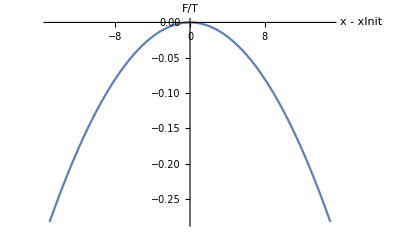

General::munfl: Exp[-1687.08] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-843.469] is too small to represent as a normalized machine number; precision may be lost.

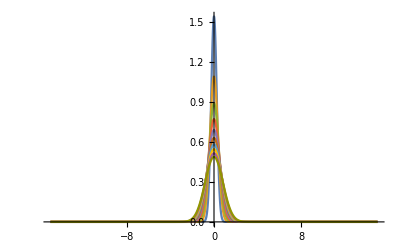

kD = 2.00386

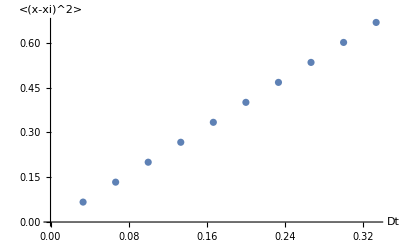

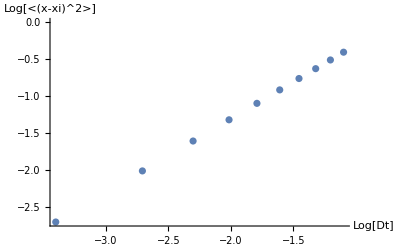

```mathematica
(*Numerical computation of a single MSD2*)
Print["1st element test: ",FullSimplify[pxList[[2]]-p1x/.{y->xi}]==0]
Plot[fFnc[x,g,x0],{x,xi-0.3/g,xi+0.3/g},PlotRange->All,AxesLabel->{"x - xInit","F/T"}]
Plot[pxList,{x,xi-0.3/g,xi+0.3/g},PlotRange->All]
msd2Data = Table[{it*d,msd2List[[it]]},{it,1,nt}];
msd2Linmodel=LinearModelFit[msd2Data,x,x];
kD=Coefficient[Normal[msd2Linmodel],x,1];
Print["kD = ",kD];
ListPlot[msd2Data,AxesLabel->{"Dt","<(x-xi)^2>"}]
ListPlot[Table[{Log[msd2Data[[it]][[1]]],Log[msd2Data[[it]][[2]]]},{it,1,nt}],AxesLabel->{"Log[Dt]","Log[<(x-xi)^2>]"}]
```

```mathematica
(*Numerical slopes for given f(x)*)
kDFnc[nt_,g_,dt_,d_,x0_,xi_]:=
Module[{p1x,x,y,pxList,i},
p1x=p1Fnc[x,dt,y,d,vFnc[x,d,g,x0]];
(*Print["v: ",vFnc[x,d,g,x0]];
Print["P1(x): ",p1x];*)
pxList={p1x/.{y->xi}};
msd2List={NExpectation[(x-xi)^2,x\[Distributed]ProbabilityDistribution[pxList[[1]],{x,-Infinity,Infinity}]]};
For[i=1,i<nt,i++,
pxNext=FullSimplify[Integrate[(pxList[[i]]/.{x->y})*p1x,{y,-Infinity,Infinity}],Assumptions->ass];
AppendTo[pxList,pxNext];
(*Print[i,": ",pxNext];*)
msd2Next=NExpectation[(x-xi)^2,x\[Distributed]ProbabilityDistribution[pxNext,{x,-Infinity,Infinity}]];
AppendTo[msd2List,msd2Next];
Print[i+1," msd2: ",msd2Next];
];
msd2Data = Table[{it*d*2,msd2List[[it]]},{it,1,nt}];
msd2Linmodel=LinearModelFit[msd2Data,x,x];
kD=Coefficient[Normal[msd2Linmodel],x,1];
kD
]

dxMax=5;
dt=1;
d=1/100;
x0=0;
xi=0;

nt=Round[dxMax^2/d];
nt = dxMax * 2;
g0=1/Sqrt[Pi*d*nt];
g0=1/50*(2/3)^(-4);
gs= Table[g0*(2/3)^i,{i,0,5}];
ng = Length[gs];
kDs=Table[0,{i,1,ng}];

Print[nt];
Print[gs];
kDs=ParallelTable[kDFnc[nt,gs[[i]],dt,d,x0,xi],{i,1,ng},Method->"FinestGrained"];

(*For[i=1,i<=ng,i++,
Print["Nt = ", nt, "; G = ", gs[[i]], "; d = ", d];
kDs[[i]]=kDFnc[nt,gs[[i]],dt,d,x0,xi];
]*)
```

10

{81/800,27/400,9/200,3/100,1/50,1/75}

2 msd2: 0.040005

2 msd2: 0.0400113

2 msd2: 0.0400255

2 msd2: 0.0400022

2 msd2: 0.0400573

2 msd2: 0.0401291

3 msd2: 0.0600106

3 msd2: 0.0600047

3 msd2: 0.0600238

3 msd2: 0.0601204

3 msd2: 0.0600535

3 msd2: 0.0602713

4 msd2: 0.0800181

4 msd2: 0.080008

4 msd2: 0.0800407

4 msd2: 0.0800917

4 msd2: 0.0802064

4 msd2: 0.0804654

5 msd2: 0.100028

5 msd2: 0.100012

5 msd2: 0.100062

6 msd2: 0.120039

6 msd2: 0.120017

6 msd2: 0.120088

5 msd2: 0.10014

7 msd2: 0.140053

7 msd2: 0.140023

7 msd2: 0.140119

5 msd2: 0.100315

5 msd2: 0.100711

8 msd2: 0.160068

8 msd2: 0.16003

8 msd2: 0.160154

9 msd2: 0.180086

9 msd2: 0.180038

9 msd2: 0.180194

10 msd2: 0.200106

10 msd2: 0.200047

6 msd2: 0.12101

6 msd2: 0.120199

6 msd2: 0.120448

$Aborted

```mathematica
(*Numerical resulting maximum deviation*)
Print[kDs];
ListPlot[Table[{Log10[gs[[i]]^2*Pi*d*nt],Log10[kDs[[i]]]},{i,1,ng}],AxesLabel->{"Log10[(F/T)(Sqrt[D t_max])]","Log10[dMSD2/d(2Dt)]"}]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

-Graphics-

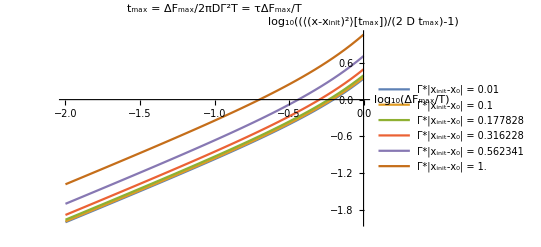

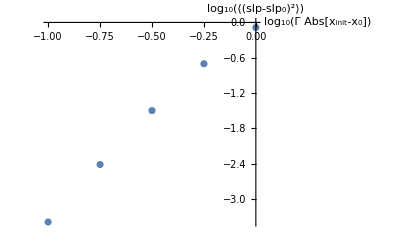

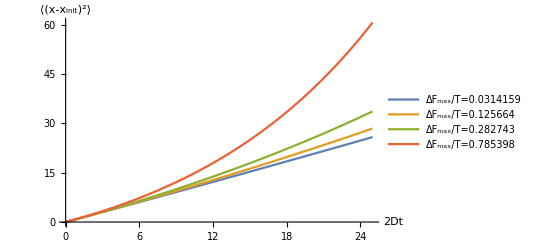

```mathematica
(*Analytical results for MSD2*)
ClearAll[a,g,d,t,b];
a[t_]:=Exp[-t];
b[t_]:=1-a[t];
sgm2[t_,g_]:=(1-a[t]^2)/(Pi*g^2);
s2[t_,g_]:=(1/a[t]^2-1)/(Pi*g^2);

rho[t_,g_,x_,x0_,xi_]:=Exp[-((x-x0)-(xi-x0)/a[t])^2/s2[t,g]]/Sqrt[Pi*s2[t,g]];

x0=0;
xi=10^-2.0;
g=1/50.0;
d=1/100.0;
fTmin=0.1^2;
fTmax=1.0^2;
lMax=5.0;
tMax=lMax^2/(2*d);
tau=1/(2*Pi*g^2*d);

xiScaleLog={-2.0,-1.0,-0.75,-0.5,-0.25,0.0};
nXi=Length[xiScaleLog];
slpList={};
slpLbls={};
dSlp={};
For[i=1,i<=nXi,i++,
AppendTo[slpList,Log10[NExpectation[(x-(1/g*10^xiScaleLog[[i]]))^2,x\[Distributed]ProbabilityDistribution[rho[10^fT,g,x,x0,(1/g*10^xiScaleLog[[i]])],{x,-Infinity,Infinity}]]/(10^fT/(Pi*g^2))-1]];
AppendTo[slpLbls,"Γ*|x_init-x_0| = "<>ToString[10^xiScaleLog[[i]]]];
If[i>1,
AppendTo[dSlp,Log10[NIntegrate[Abs[slpList[[1]]-slpList[[i]]]^2,{fT,Log10[fTmin],Log10[fTmax]}]]];
];
]
Plot[slpList,{fT,Log10[fTmin],Log10[fTmax]},PlotLabel->"t_max = ΔF_max/2πDΓ^2T = τΔF_max/T",AxesLabel->{TraditionalForm[Style[HoldForm[Log10[Subscript[ΔF, max]/T]]]],TraditionalForm[Style[HoldForm[Log10[AngleBracket[(x - Subscript[x, init])^2][Subscript[t, max]]/(2 D Subscript[t, max]) - 1]]]]},PlotLegends->slpLbls]
ListPlot[Table[{xiScaleLog[[i]],dSlp[[i-1]]},{i,2,nXi}],AxesLabel->{TraditionalForm[Style[HoldForm[Log10[Γ*Abs[Subscript[x, init]-Subscript[x, 0]]]]]],TraditionalForm[Style[HoldForm[Log10[AngleBracket[(slp - Subscript[slp, 0])^2]]]]]}]

Manipulate[
Module[{gLocal,lBigLocal,xiLocal,tLocal,dLocal,xRangeLocal,tauLocal},
gLocal=10^gLocalLog;
dLocal=10^dLocalLog;
xiLocal=1/gLocal*10^xiLocalScaleLog;
lBigLocal=1/Sqrt[(Pi*gLocal^2)];
tauLocal=1/(2*Pi*gLocal^2*dLocal);
tLocal=(10^tLocalScaleLog)*tauLocal;
xRangeLocal=Sqrt[2*dLocal*tLocal]*10^xRangeLog;
Plot[rho[tLocal/tauLocal,gLocal,x/gLocal,x0,xiLocal],{x,(xiLocal-xRangeLocal)*gLocal,(xiLocal+xRangeLocal)*gLocal},AxesLabel->{"G*(x-x0)","rhoX"},PlotLabel->"t/tau = "<>ToString[tLocal/tauLocal],PlotRange->All]],
{{gLocalLog,Log10[g]},Log10[g]-2,Log10[g]+2},
{{xiLocalScaleLog,Log10[xi*g]},Log10[xi*g]-1,0},
{{tLocalScaleLog,-1},-5,5},
{{dLocalLog,Log10[d]},Log10[d]-5,Log10[d]+5},
{{xRangeLog,1},-1,2}]

Manipulate[
Module[{gLocal, xiLocal},
gLocal=10^gLocalLog;
xiLocal = 1/gLocal*10^xiLocalScaleLog;
Plot[Log10[NExpectation[(x-xiLocal)^2,x\[Distributed]ProbabilityDistribution[rho[10^fT,gLocal,x,x0,xiLocal],{x,-Infinity,Infinity}]]/(10^fT/(Pi*gLocal^2))-1],{fT,Log10[fTmin],Log10[fTmax]},PlotLabel->"t_max=ΔF_max/2πDΓ^2T",AxesLabel->{TraditionalForm[Style[HoldForm[Log10[Subscript[ΔF, max]/T]]]],TraditionalForm[Style[HoldForm[Log10[AngleBracket[(x - Subscript[x, init])^2][Subscript[t, max]]/(2 D Subscript[t, max]) - 1]]]]}]],{{gLocalLog,Log10[g]},Log10[g]-2,Log10[g]+2},{{xiLocalScaleLog,Log10[xi*g]},Log10[xi*g]-5,1}]

Manipulate[
Module[{gLocal,dLocal,tMaxLocal,xiLocal},
gLocal=10^gLocalLog;
dLocal=10^dLocalLog;
tMaxLocal=lMaxLocal^2/(2*dLocal);
xiLocal = 1/gLocal*10^xiLocalScaleLog;
Plot[NExpectation[(x-xiLocal)^2,x\[Distributed]ProbabilityDistribution[rho[t*(Pi*gLocal^2),gLocal,x,x0,xiLocal],{x,-Infinity,Infinity}]],{t,0,tMaxLocal*2*dLocal},AxesLabel->{"2Dt",TraditionalForm[Style[HoldForm[AngleBracket[(x - Subscript[x, init])^2]]]]},PlotLabel->TraditionalForm[Style[Row[{HoldForm[ΔF[√(2D Subscript[t, max])]/T],"=",tMaxLocal*2*dLocal*Pi*gLocal^2}]]]]],{{gLocalLog,Log10[g]},Log10[g]-2,Log10[g]+2},
{{dLocalLog,Log10[d]},Log10[d]-2,Log10[d]+2},
{{lMaxLocal,lMax},0,50},{{xiLocalScaleLog,Log10[xi*g]},Log10[xi*g]-5,1}]

gs={g,g*2, g*3,g*5};
ng=Length[gs];
msdList=Table[NExpectation[(x-xi)^2,x\[Distributed]ProbabilityDistribution[rho[t*(Pi*gs[[i]]^2),gs[[i]],x,x0,xi],{x,-Infinity,Infinity}]],{i,1,ng}];
Plot[msdList,{t,0,tMax*2*d},AxesLabel->{"2Dt",TraditionalForm[Style[HoldForm[AngleBracket[(x - Subscript[x, init])^2]]]]},PlotLegends->Table[TraditionalForm[Style[Row[{HoldForm[Subscript[ΔF, max]/T],"=",tMax*2*d*(Pi*gs[[i]]^2)}]]],{i,1,ng}]]
```

f(w)=A/(√((1-w^2) (a^2-w^2)))ζ=ξ+η ⅈ=∫_0^z A/(√((1-w^2) (a^2-w^2)))ⅆwη=∫1/(R+ρ cos(t))ⅆt
ξ=ϕ

F/T(x)=-πΓ^2 (x-x_0)^2=0.4

f(x)=-πΓ^2 (x-x_0)^2

F(r)→-(∂f)/(∂x)

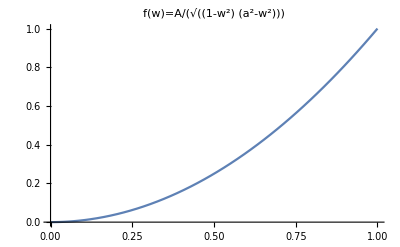

```mathematica
(*Legend construction tests*)
Style[Row[{Spacer[60],HoldForm[f[w]=A/Sqrt[(1-w^2) (a^2-w^2)]],Spacer[150],HoldForm[ζ=ξ+η I=Integrate[A/(Sqrt[(1-w^2) (a^2-w^2)]),{w," 0"," z"}]],Spacer[100],Column[{HoldForm[η=Integrate[1/(R+ρ Cos[t]),t]],HoldForm[ξ=ϕ]}],Spacer[20]}],20]//TraditionalForm

Style[Row[{HoldForm[(F/T)[x]=-πΓ^2(x-Subscript[x, 0])^2],"=",1.2/3}]]//TraditionalForm
Style[Row[{HoldForm[f[x]=-πΓ^2(x-Subscript[x, 0])^2]}]]//TraditionalForm
Style[Row[{HoldForm[F[r]->-D[f,x]]}]]//TraditionalForm
Plot[x^2,{x,0,1},PlotLabel->(TraditionalForm[Style[HoldForm[f[w]=A/Sqrt[(1-w^2) (a^2-w^2)]]]])]
```

```mathematica
AngleBracket[P]
```

⟨P⟩

```mathematica
(*Check that my solution satisfies the equation*)
ClearAll[a,g,d,t,b,x0,xi,rho,s2,sgm2];
a[t_]:=Exp[-t];
b[t_]:=1-a[t];
sgm2[t_,g_]:=(1-a[t]^2)/(Pi*g^2);
s2[t_,g_]:=(1/a[t]^2-1)/(Pi*g^2);
f[x_,x0_, g_]:=-Pi*g^2*(x-x0)^2;

rho[t_,g_,x_,x0_,xi_]:=Exp[-((x-x0)+(x0-xi)/a[t])^2/s2[t,g]]/Sqrt[Pi*s2[t,g]];

tau=1/(2*Pi*d*g^2);
FullSimplify[d*(D[rho[t/tau,g,x,x0,xi],{x,2}]+D[rho[t/tau,g,x,x0,xi],{x,1}]*D[f[x,x0,g],{x,1}]+rho[t/tau,g,x,x0,xi]*D[f[x,x0,g],{x,2}])-D[rho[t/tau,g,x,x0,xi],{t,1}]]
```

0